```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.1,Jtwo,0.3,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.8850612031567836}]
```

{z→0.885061}

```mathematica
Clear[IntPlus,NullsHolm,G,P]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))/.{J->1,q->0.1,l->0.3}
```

0.842615+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
p= Check[FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
],z->0];
AppendTo[lst,{Jtwoo,p}];
,{n,1,199,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,200,1}];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.8426149773176358]]
```

{{0.005,0.845429},{0.01,0.847974},{0.015,0.850233},{0.02,0.852192},{0.025,0.853835},{0.03,0.855149},{0.035,0.856125},{0.04,0.856754},{0.045,0.857032},{0.05,0.856957},{0.055,0.856531},{0.06,0.85576},{0.065,0.854652},{0.07,0.853217},{0.075,0.851469},{0.08,0.849423},{0.085,0.847092},{0.09,0.844494},{0.095,0.841644},{0.1,0.838558}}

```mathematica
moduler[Lister[-1,-0.005,0.8426149773176358]]
```

{{-0.005,0.839548},{-0.01,0.836244},{-0.015,0.832718},{-0.02,0.828986},{-0.025,0.82506},{-0.03,0.820954},{-0.035,0.816679},{-0.04,0.812245},{-0.045,0.807663},{-0.05,0.80294},{-0.055,0.798086},{-0.06,0.793105},{-0.065,0.788005},{-0.07,0.78279},{-0.075,0.777466},{-0.08,0.772036},{-0.085,0.766505},{-0.09,0.760874},{-0.095,0.755147},{-0.1,0.749325}}

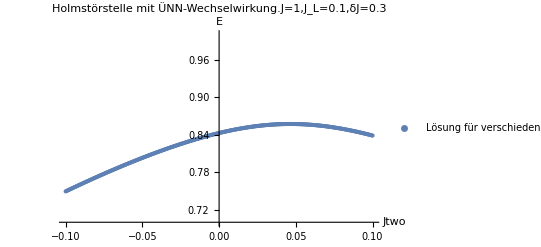

```mathematica
G =ListPlot[Fueger[moduler[Lister[1,0.0005,0.8426149773176358]],moduler[Lister[-1,-0.0005,0.8426149773176358]]],AxesLabel->{Jtwo,"E"},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.1,δJ=0.3",PlotRange->{0.7,1}]
```

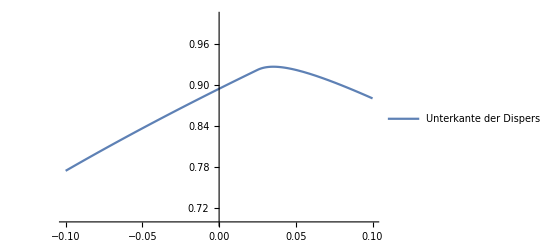

```mathematica
P =Plot[Sqrt[1+2(0.1*Cos[Inv[0.1,Jtwo]]+Jtwo*Cos[2*Inv[0.1,Jtwo]])],{Jtwo,-0.1,0.1},PlotRange->{0.7,1},PlotLegends->{"Unterkante der Dispersion"}]
```

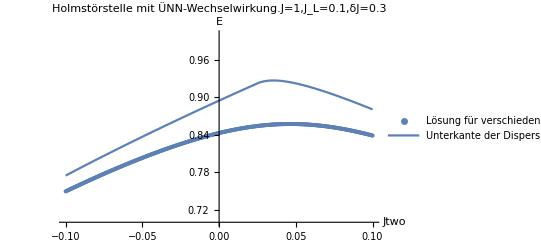

```mathematica
Show[G,P]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.0005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
differ[-1,0.1,moduler[Lister[-1,-0.005,0.8426149773176358]]]
```

{{-0.005,0.0492715},{-0.01,0.0469321},{-0.015,0.044778},{-0.02,0.0427938},{-0.025,0.0409652},{-0.03,0.0392786},{-0.035,0.0377216},{-0.04,0.0362829},{-0.045,0.034952},{-0.05,0.0337195},{-0.055,0.0325768},{-0.06,0.0315162},{-0.065,0.0305306},{-0.07,0.0296137},{-0.075,0.0287597},{-0.08,0.0279636},{-0.085,0.0272208},{-0.09,0.0265269},{-0.095,0.0258784},{-0.1,0.0252717}}

```mathematica
differ[1,0.1,moduler[Lister[1,0.005,0.8426149773176358]]]
```

{{0.005,0.054571},{0.01,0.0575647},{0.015,0.0608102},{0.02,0.0643236},{0.025,0.264199},{0.03,0.0704137},{0.035,0.0704662},{0.04,0.0692587},{0.045,0.0673296},{0.05,0.0649974},{0.055,0.0624603},{0.06,0.0598454},{0.065,0.0572356},{0.07,0.0546846},{0.075,0.0522268},{0.08,0.0498828},{0.085,0.0476638},{0.09,0.0455745},{0.095,0.0436152},{0.1,0.0417828}}

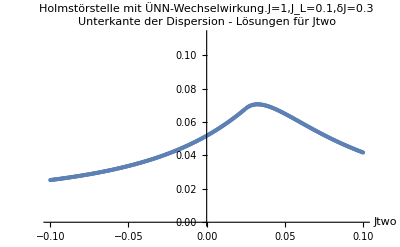

```mathematica
ListPlot[Fueger[differ[-1,0.1,moduler[Lister[-1,-0.0005,0.8426149773176358]]],differ[1,0.1,moduler[Lister[1,0.0005,0.8426149773176358]]]],AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.1,δJ=0.3"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.87141}. NIntegrate obtained -0.179235 and 0.277837 for the integral and error estimates.

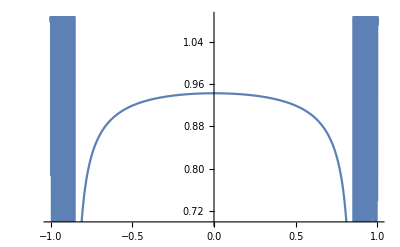

```mathematica
Plot[NullsHolm[-0.035,z],{z,-1,1}]
```